```mathematica
Directory[]
results0=Import["manuscripts/IPD_Predictor/results0.txt","Table", "FieldSeparators"->","];
results=Import["manuscripts/IPD_Predictor/results1.txt","Table","FieldSeparators"->","];
places = Import["manuscripts/IPD_Predictor/results2.txt","Table","FieldSeparators"->","];

results[[1]]
results0[[2;;22,1]]
places = 11-places[[2;;22,1;;10]];
places[[1]]
```

/Users/prentner

{explore, PREDICTOR, RANDOM, ZD-GTFT-2, TFT, WSLS, ALLD, ZD-Extort-2, JOSS, GTFT, ALLC, }

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.}

{9.,4.,8.,7.,6.,2.,1.,3.,10.,5.}

```mathematica
place={1,0.57};
plotIPD=ListPlot[Transpose[{results0[[2;;22,1]],results0[[2;;22,2]]}],InterpolationOrder->None,PlotRange->All,PlotStyle->Thick,Joined->True,PlotMarkers->{Automatic},PlotLegends->Placed[SwatchLegend[{"TOTAL"}],place]]
IPD=Transpose[{results0[[2;;22,1]],results0[[2;;22,2]]}];
PRE=Transpose[{results[[2;;22,1]],results[[2;;22,2]]}];
RAND = Transpose[{results[[2;;22,1]],results[[2;;22,3]]}];
ZDG=Transpose[{results[[2;;22,1]],results[[2;;22,4]]}];
TFT = Transpose[{results[[2;;22,1]],results[[2;;22,5]]}];
WSLS=Transpose[{results[[2;;22,1]],results[[2;;22,6]]}];
ALLD = Transpose[{results[[2;;22,1]],results[[2;;22,7]]}];
ZDE = Transpose[{results[[2;;22,1]],results[[2;;22,8]]}];
JOSS = Transpose[{results[[2;;22,1]],results[[2;;22,9]]}];
GTFT = Transpose[{results[[2;;22,1]],results[[2;;22,10]]}];
ALLC = Transpose[{results[[2;;22,1]],results[[2;;22,11]]}];
score=ListPlot[{IPD, PRE,TFT,GTFT,ZDE},Joined->True,InterpolationOrder->{None,2,2,2,2,2},PlotStyle->{Thick,Dotted,Dotted,Dotted,Dotted,Dotted},PlotMarkers->{Automatic,None,None,None,None,None},PlotLegends->Placed[SwatchLegend[{"TOTAL","SELF","TFT","GTFT","ZD-EXTORT-2","ALLC"}],place],PlotRange->{All,{0.75,3.25}},Frame->True,Axes->False, FrameLabel->{"exploration","payoff"},LabelStyle->{14,FontFamily->"Times"},ImageSize->500]
Export["manuscripts/IPD_PREDICTOR/score.pdf",score]
```

-Graphics-

-Graphics-

manuscripts/IPD_PREDICTOR/score.pdf

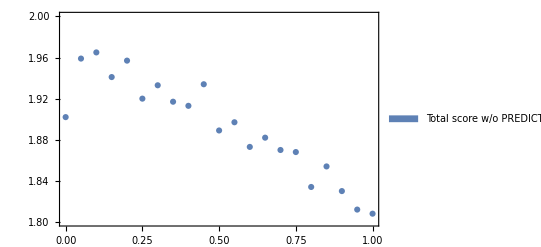

1.91333+0.791881 x-4.73993 x^2+10.3448 x^3-10.1105 x^4+3.60971 x^5

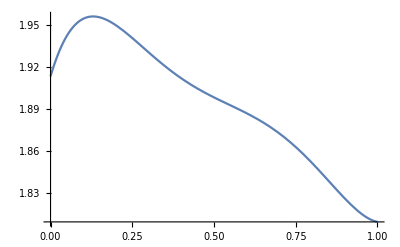

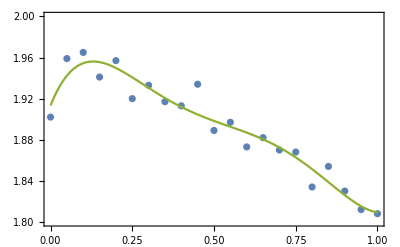

manuscripts/IPD_PREDICTOR/score_alt.pdf

```mathematica
data = Transpose[{results[[2;;22,1]],results0[[2;;22,2]]-0.1*(results[[2;;22,11]]+results[[2;;22,7]])}];
plotalt=ListPlot[ data,InterpolationOrder->None,PlotMarkers->{Automatic},PlotStyle->{ColorData[97,1],Thick},PlotRange->{All,{1.8,2}},Frame->True,Axes->False,PlotLegends->SwatchLegend[{"Total score w/o PREDICTOR and ALLC"}]]

poly = Fit[data, {1,x,x^2,x^3,x^4,x^5},x]
Plot[poly, {x, 0, 1}]
scorealt=Show[ListPlot[data], Plot[poly, {x, 0, 1},PlotStyle->ColorData[97,3]],PlotRange->{All,{1.8,2}},Frame->True,Axes->False]
Export["manuscripts/IPD_PREDICTOR/score_alt.pdf",scorealt]
```

```mathematica
results[[1]]
PRE= Transpose[{results[[2;;22,1]],places[[1;;21,1]]}];
RAND= Transpose[{results[[2;;22,1]],places[[1;;21,2]]}];
ZDG= Transpose[{results[[2;;22,1]],places[[1;;21,3]]}];
TFT= Transpose[{results[[2;;22,1]],places[[1;;21,4]]}];
WSLS = Transpose[{results[[2;;22,1]],places[[1;;21,5]]}];
ALLD=Transpose[{results[[2;;22,1]],places[[1;;21,6]]}];
ZDE=Transpose[{results[[2;;22,1]],places[[1;;21,7]]}];
JOSS= Transpose[{results[[2;;22,1]],places[[1;;21,8]]}];
GTFT =Transpose[{results[[2;;22,1]],places[[1;;21,9]]}];
ALLC= Transpose[{results[[2;;22,1]],places[[1;;21,10]]}];
tickSpecification=Table[{i,11-i},{i,2,10,2}]
plotPRE=ListLinePlot[{PRE,ZDG,TFT,GTFT,ZDE,ALLC,JOSS},InterpolationOrder->0,FrameTicks->{{tickSpecification,None},Automatic},PlotRange->{All,{0.5,10.5}},Frame->True,Axes->False,Mesh->All,PlotStyle->{Thick,Thin,Thin,Thin,Thin,Thin,Thin},PlotLegends->Placed[SwatchLegend[{"PREDICTOR","ZD-GTFT-2","TFT","GTFT","ZD-EXTORT-2","ALLC","JOSS"}],place],FrameLabel->{"exploration","place"},LabelStyle->{14,FontFamily->"Times"},ImageSize->500]
Export["manuscripts/IPD_PREDICTOR/plotpre.pdf",plotPRE]
```

{explore, PREDICTOR, RANDOM, ZD-GTFT-2, TFT, WSLS, ALLD, ZD-Extort-2, JOSS, GTFT, ALLC, }

{{2,9},{4,7},{6,5},{8,3},{10,1}}

-Graphics-

manuscripts/IPD_PREDICTOR/plotpre.pdf

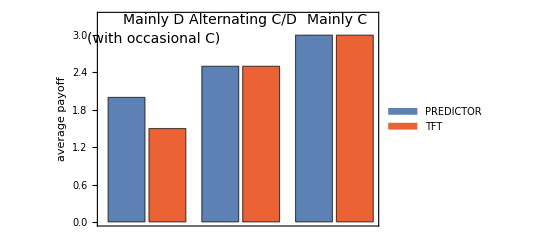

manuscripts/IPD_PREDICTOR/tft.pdf

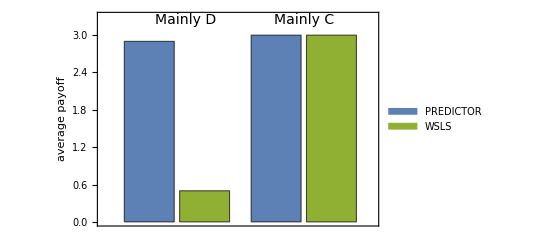

manuscripts/IPD_PREDICTOR/wsls.pdf

```mathematica
ColorData[97];
TFT={{2.0,1.5},{2.5,2.5},{3.,3}};
WSLS={{2.9,0.5},{3.,3.}};
tft = BarChart[TFT,PlotRange->{All,{-0.,3.3}},Frame->True,Axes->False,ChartStyle->{ColorData[97,1],ColorData[97,4]},ChartLegends->{"PREDICTOR","TFT"},FrameLabel->{None,"average payoff"},LabelStyle->{14,FontFamily->"Times"},ImageSize->400,
Epilog->{Text[Style["Mainly D",14,FontFamily->"Times"],{1.85,3.25}],
Text[Style["(with occasional C)",14,FontFamily->"Times"],{1.85,2.95}],Text[Style["Alternating C/D",14,FontFamily->"Times"],{4.05,3.25}],
Text[Style["Mainly C",14,FontFamily->"Times"],{6.35,3.25}]}]
Export["manuscripts/IPD_PREDICTOR/tft.pdf",tft]

wsls = BarChart[WSLS,PlotRange->{All,{-0.,3.3}},Frame->True,Axes->False,ChartStyle->{ColorData[97,1],ColorData[97,3]},ChartLegends->{"PREDICTOR","WSLS"},FrameLabel->{None,"average payoff"},LabelStyle->{14,FontFamily->"Times"},ImageSize->400,
Epilog->{Text[Style["Mainly D",14,FontFamily->"Times"],{1.85,3.25}],Text[Style["Mainly C",14,FontFamily->"Times"],{4.0,3.25}]}]
Export["manuscripts/IPD_PREDICTOR/wsls.pdf",wsls]
 (*PlotStyle->{Thick,Thin,Thin,Thin,Thin,Thin,Thin},PlotLegends->Placed[SwatchLegend[{"PREDICTOR","ZD-GTFT-2","TFT","GTFT","ZD-EXTORT-2","ALLC","JOSS"}],place],FrameLabel->{"exploration","place"},LabelStyle->{14,FontFamily->"Times"},ImageSize->500]*)
```

5

{0.0559,0.0592,0.0578,0.0582,0.0633,0.0655,0.0651,0.0646,0.0632,0.0662,0.0637,0.0642,0.0657,0.0661,0.0665,0.0627,0.063,0.0653,0.0642,0.0639,0.0654,0.0634,0.0639,0.0642,0.0646,0.0629,0.0629,0.0661,0.0646,0.0645,0.0631,0.0648,0.0637,0.0643,0.0652,0.0635,0.0647,0.0665,0.0651,0.0626}

0.0666683-0.0103332/(√x)

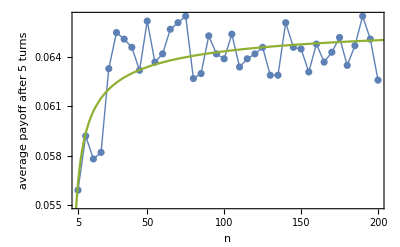

manuscripts/IPD_PREDICTOR/score_alt.pdf

```mathematica
data={0.115,0.117,0.116,0.115,0.096,0.113,0.12,0.114,0.124,0.121,0.111,0.11,0.119,0.12,0.118,0.105,0.136,0.121,0.09,0.13,0.107,0.144,0.13,0.129,0.123,0.134,0.126,0.125,0.131,0.139,0.12,0.133,0.134,0.127,0.137,0.126,0.134,0.129,0.129,0.128,0.125,0.13,0.117,0.13,0.13,0.138,0.129,0.134,0.133,0.128,0.127,0.121,0.131,0.132,0.126,0.127,0.127,0.127,0.134,0.127,0.134,0.132,0.134,0.121,0.136,0.137,0.138,0.129,0.133,0.124,0.135,0.132,0.136,0.136,0.126,0.126,0.121,0.128,0.135,0.117,0.127,0.136,0.119,0.12,0.128,0.132,0.128,0.132,0.132,0.129,0.13,0.125,0.132,0.125,0.13,0.13,0.132,0.132,0.121,0.124,0.132,0.14,0.125,0.128,0.129,0.128,0.126,0.124,0.128,0.128,0.128,0.129,0.129,0.128,0.125,0.132,0.126,0.128,0.128,0.128,0.128,0.128,0.128,0.129,0.133,0.121,0.124,0.128,0.128,0.128,0.13,0.126,0.124,0.117,0.132,0.136,0.132,0.133,0.132,0.128,0.136,0.121,0.132,0.129,0.128,0.121,0.125,0.133,0.129,0.137,0.133,0.122,0.121,0.126,0.129,0.132,0.132,0.132,0.124,0.128,0.124,0.121,0.124,0.136,0.132,0.133,0.132,0.125,0.124,0.129,0.132,0.132,0.124,0.136,0.128,0.122,0.128,0.128,0.125,0.132,0.125,0.129,0.128,0.136,0.129,0.136,0.125,0.136,0.132,0.136,0.132,0.128,0.133,0.133,0.125,0.117,0.122,0.129,0.128,0.13};
nt = 5
score = Table[Total[data[[1+(j-1)*nt;;j*nt]]],{j,1,200/nt}] /10
fitscore = Fit[score,{1,1/Sqrt[x]},x]
tickSpecification = {{1,5},{10,50},{20,100},{30,150},{40,200}};
scorealt = Show[ListPlot[score,Mesh->All,InterpolationOrder->1,PlotStyle->Thin,Joined->True,PlotRange->All], Plot[fitscore, {x, -100, 200},PlotStyle->ColorData[97,3],PlotRange->All],PlotRange->{{1,200/nt},{0.055,0.0665}},Axes->False,Frame->True,FrameLabel->{Style["n",Italic],"average payoff after 5 turns"},LabelStyle->{14,FontFamily->"Times"},
FrameTicks->{{{0.055,0.058,0.061,0.064,0.067},None},{tickSpecification,None}},
ImageSize->400]
Export["manuscripts/IPD_PREDICTOR/score_alt.pdf",scorealt]
```